```mathematica
L2[n_,1,b_]:=L2[n,1,b]=Sum[Log[j],{j,2,n}]-b Sum[Log[j b],{j,1,n/b}]
L2[n_,k_,b_]:=Sum[L2[n/j,k-1,b],{j,2,n}]-b Sum[L2[n/(j b),k-1,b],{j,1,n}]
L1[n_, z_, b_] := Sum[ Binomial[z,k]L2[n,k,b],{k,0,Log[If[b<2,b,2],n]}]
sa[n_,c_] := Sum[c^k Log[c],{k,1,Log[c,n]}]
```

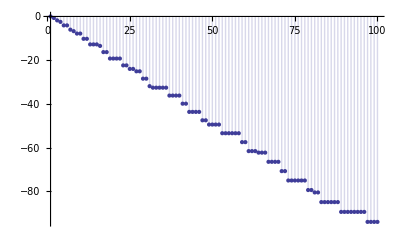

```mathematica
DiscretePlot[L1[n,-1,2]-sa[n,2],{n,1,100}]
```

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
D1xD[n_,s_,k_,x_]:=D1xD[n,s,k,x]=Sum[(j+1)^-s D1xD[n/(j+1),s,k-1,x]-x (j x)^-s D1xD[n/(x j),s,k-1,x],{j,1,n}]
D1xD[n_,s_,0,x_]:=UnitStep[n-1]
DxD[n_,s_,z_,x_]:=Sum[bin[z,k] D1xD[n,s,k,x],{k,0,If[x<2,Log[x,n],Log[2,n]]}]

N[D[FullSimplify@D1xD[100,s,2,2],s]/.s->0]
```

-12.8961

```mathematica
-2N@L2[100,2,2]
```

-12.8961

```mathematica
D[Expand@N[D[DxD[100,s,z,2],s]/.s->0],z]/.z->0
```

-6.70877

```mathematica
N@L1[100,-1,2]
```

-6.70877